# Chapter 1: Kolmogorovian axiomatization

## Conditional probability

Def. Given a probability space (Ω,ℱ,P) and two events A,B∈ℱ with P{B}≠0, we will call conditional probability of A wrt B

P{A|B}=(P{A∧B})/(P{B})=(P{AB})/(P{B})

with P{AB} takes the name of joint probability of A and B.

(Ω,ℱ,P(|B)) is also a probability space.

Prop. Total probability formula. Given a probability space (Ω,ℱ,P), an event A∈ℱ, and  a decomposition 𝒟={D_n}_nwith P{B}≠0,

P{A}=∑_(j=1)^n P{A|D_j}P{D_j}

Indeed,

P{A}=P{A∧Ω}=P{A∧(∨_j D_j)}=P{∨_j(A∧D_j)}=∑_(j=1)^n P{A∧D_j}=∑_(j=1)^n P{A|D_j}P{D_j}.

## when what has already happened matters

-Graphics-

## Multiplication formula - Bayes theorem

Def. Given a probability space (Ω,ℱ,P) and the events A_1,...,A_n∈ℱ with P{A_1,...,A_n}≠0,

P{A_n,A_(n-1),...,A_1}=P{A_n|A_(n-1),...,A_1}P{A_(n-1)|A_(n-2),...,A_1}...P{A_2|A_1}P{A_1}

indeed,

P{A_n,A_(n-1),...,A_1}(P{A_n|A_(n-1),...,A_1})/(P{A_n,A_(n-1),...,A_1})(P{A_(n-1)|A_(n-2),...,A_1})/(P{A_n|A_(n-1),...,A_1})...(P{A_2|A_1})/(P{A_1})P{A_1}=P{A_n,A_(n-1),...,A_1}.

Prop. Bayes theorem. Given a probability space (Ω,ℱ,P) and two events A,B∈ℱ with P{A},P{B}≠0,

P{A|B}=(P{B|A}P{A})/(P{B})

indeed,

P{A|B}P{B}=P{B|A}P{A}=P{AB}

## Independent events

Def. Given a probability space (Ω,ℱ,P), we say that A,B∈ℱ are independent events when

P{A|B}=P{A}

or equivalently,

P{AB}=P{A|B}P{B}=P{A}P{B}

# Chapter 2: Well-known measures

## Binomial distribution ℬ(n;p)

p_n(k)=(n
k)p^k q^(n-k),  k≤n.

See the documentation, or in the notes. (Expand Task 2)

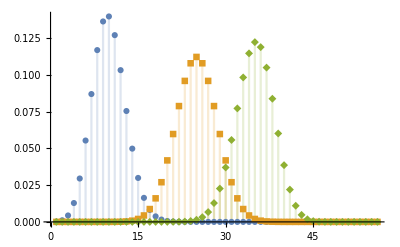

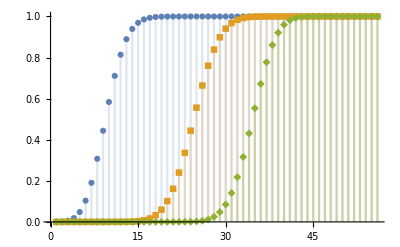

```mathematica
plot[n_,p1_,p2_,p3_]:=DiscretePlot[Evaluate[Table[PDF[BinomialDistribution[n, p], k], {p, {p1, p2, p3}}]], {k, 56}, PlotRange -> All, PlotMarkers -> Automatic]
plot[50,.2,.5,.7]
plot[n_,p1_,p2_,p3_]:=DiscretePlot[Evaluate[Table[CDF[BinomialDistribution[n, p], k], {p, {p1, p2, p3}}]], {k, 56}, PlotRange -> All, PlotMarkers -> Automatic]
plot[50,.2,.5,.7]
```

## Multinomial distribution ℬ(n;p_0,...,p_r)

p_n(k_0,...,k_r)=(n
k_0,...,k_r)p_0^k_0... p_r^k_r,  ∑_(i=0)^r k_i=n,  ∑_(i=0)^r p_i=1.

See the documentation, or in the notes. (Expand Task 2)

```mathematica
Table[DiscretePlot3D[PDF[MultinomialDistribution[n, {0.6, 0.4}], {x, y}], {y, 0, n}, {x, 0, n}, PlotLabel -> Row[{"n = ", n}], ExtentSize -> 0.5], {n, {3, 6, 9, 12}}]
Table[DiscretePlot3D[CDF[MultinomialDistribution[n, {0.6, 0.4}], {x, y}], {y, 0, n}, {x, 0, n}, PlotLabel -> Row[{"n = ", n}], ExtentSize -> 0.5], {n, {3, 6, 9, 12}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Poisson distribution 𝒫(α)

Given (ℕ,𝒫(ℕ),p_α) (Expand Task 2)

p_α(k)=ⅇ^-α α^k/(k!),   α>0

See the documentation, or in the notes. (Expand Task 2)

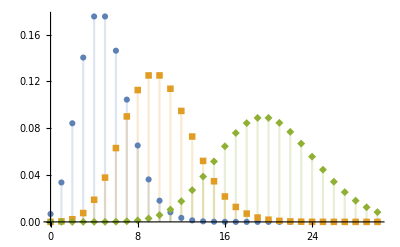

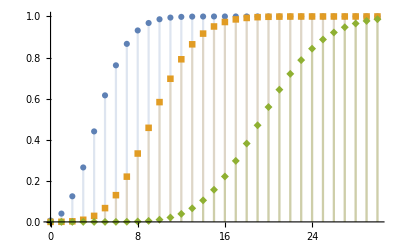

```mathematica
DiscretePlot[Evaluate[Table[PDF[PoissonDistribution[α], k], {α, {5, 10, 20}}]], {k, 0, 30}, PlotRange -> All, PlotMarkers -> Automatic]
DiscretePlot[Evaluate[Table[CDF[PoissonDistribution[α], k], {α, {5, 10, 20}}]], {k, 0, 30}, PlotRange -> All, PlotMarkers -> Automatic]
```

## Probability on ℝ

### Cumulative distribution functions

Given (ℝ,ℬ(ℝ),P) we call cumulative distributions functions

F(x)=P{(-∞;x]}    for all x∈ℝ such that 
(i) F is non decreasing; 
(ii) F(-∞)=0, F(+∞)=1;
(iii) F is right continuous with left limits forall x∈ℝ (well defined - see the notes)

Prop.

P{(b;a]}=F(a)-F(b)  for -∞≤b≤a≤+∞.

-Graphics-

## Section six

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy.
		Lorem Ipsum